```mathematica
x1=-1/2;x2=-3/2;x3=-x1-x2;
a=x1 x2 + x2 x3 + x1 x3
b=-x1 x2 x3
Solve[x^3+a x +b ==0 ,x]
sol=Simplify[Solve[{1+α^2+β^2==-a,2 α β == -b },{α,β}]]
```

-13/4

-3/2

{{x→-3/2},{x→-1/2},{x→2}}

{{α→-1/2 √(3/2 (3-√5)),β→-1/8 √(18-6 √5) (3+√5)},{α→1/2 √(3/2 (3-√5)),β→1/8 √(18-6 √5) (3+√5)},{α→-1/2 √(3/2 (3+√5)),β→1/4 (-3+√5) √(3/2 (3+√5))},{α→1/2 √(3/2 (3+√5)),β→-1/4 (-3+√5) √(3/2 (3+√5))}}

```mathematica
H=({{0, 1, α}, {1, 0, β}, {α, β, 0}});
```

```mathematica
FullSimplify[MatrixExp[ⅈ H z/.sol[[4]]]]//TraditionalForm
```

(1/140 ⅇ^(-(3 ⅈ z)/2) (15 (3+√5)-7 (-7+3 √5) ⅇ^(ⅈ z)+(46+6 √5) ⅇ^((7 ⅈ z)/2)) | 1/70 ⅇ^(-(3 ⅈ z)/2) (-15-7 ⅇ^(ⅈ z)+22 ⅇ^((7 ⅈ z)/2)) | 1/70 √(3/2 (3+√5)) ⅇ^(-(3 ⅈ z)/2) (-5 √5+7 (-2+√5) ⅇ^(ⅈ z)-2 (-7+√5) ⅇ^((7 ⅈ z)/2))
1/70 ⅇ^(-(3 ⅈ z)/2) (-15-7 ⅇ^(ⅈ z)+22 ⅇ^((7 ⅈ z)/2)) | 1/140 ⅇ^(-(3 ⅈ z)/2) (-15 (-3+√5)+7 (7+3 √5) ⅇ^(ⅈ z)+(46-6 √5) ⅇ^((7 ⅈ z)/2)) | 1/140 √(3/2 (3+√5)) ⅇ^(-(3 ⅈ z)/2) (5 (-5+3 √5)-7 (1+√5) ⅇ^(ⅈ z)-8 (-4+√5) ⅇ^((7 ⅈ z)/2))
1/70 √(3/2 (3+√5)) ⅇ^(-(3 ⅈ z)/2) (-5 √5+7 (-2+√5) ⅇ^(ⅈ z)-2 (-7+√5) ⅇ^((7 ⅈ z)/2)) | 1/140 √(3/2 (3+√5)) ⅇ^(-(3 ⅈ z)/2) (5 (-5+3 √5)-7 (1+√5) ⅇ^(ⅈ z)-8 (-4+√5) ⅇ^((7 ⅈ z)/2)) | 1/70 ⅇ^(-(3 ⅈ z)/2) (25+21 ⅇ^(ⅈ z)+24 ⅇ^((7 ⅈ z)/2)))

```mathematica
First we calculate the five capital 'Greeks' from the two sets of linear diff equations as was derived in sec 2 in the paper
```

```mathematica
sol1=FullSimplify[DSolve[Join[Thread[Flatten[({{Θ'[z]}, {Δ'[z]}, {Γ'[z]}})]==Flatten[ⅈ (H/.sol[[4]]).({{Θ[z]}, {Δ[z]}, {Γ[z]}})]],{Γ[0]==1,Δ[0]==0,Θ[0]==0}],{Γ[z],Δ[z],Θ[z]},z]]
sol2=FullSimplify[DSolve[Join[Thread[Flatten[({{Σ'[z]}, {Π'[z]}, {Δ'[z]}})]==Flatten[ⅈ (H/.sol[[4]]).({{Σ[z]}, {Π[z]}, {Δ[z]}})]],{Σ[0]==0,Π[0]==1,Δ[0]==0}],{Σ[z],Π[z],Δ[z]},z]]
```

{{Γ[z]→1/70 ⅇ^(-(3 ⅈ z)/2) (25+21 ⅇ^(ⅈ z)+24 ⅇ^((7 ⅈ z)/2)),Δ[z]→1/140 √(3/2 (3+√5)) ⅇ^(-(3 ⅈ z)/2) (5 (-5+3 √5)-7 (1+√5) ⅇ^(ⅈ z)-8 (-4+√5) ⅇ^((7 ⅈ z)/2)),Θ[z]→1/70 √(3/2 (3+√5)) ⅇ^(-(3 ⅈ z)/2) (-5 √5+7 (-2+√5) ⅇ^(ⅈ z)-2 (-7+√5) ⅇ^((7 ⅈ z)/2))}}

{{Δ[z]→1/140 √(3/2 (3+√5)) ⅇ^(-(3 ⅈ z)/2) (5 (-5+3 √5)-7 (1+√5) ⅇ^(ⅈ z)-8 (-4+√5) ⅇ^((7 ⅈ z)/2)),Π[z]→1/140 ⅇ^(-(3 ⅈ z)/2) (-15 (-3+√5)+7 (7+3 √5) ⅇ^(ⅈ z)+(46-6 √5) ⅇ^((7 ⅈ z)/2)),Σ[z]→1/70 ⅇ^(-(3 ⅈ z)/2) (-15-7 ⅇ^(ⅈ z)+22 ⅇ^((7 ⅈ z)/2))}}

### Now we calculate the same five ‘Greeks’ via the third order diff equation as was done in sec 3

```mathematica
Dsol=FullSimplify[DSolve[{(ⅈ Δ'''[z]+ⅈ(1+α^2+β^2)Δ'[z]-2 α β Δ[z]==0),Δ[0]==0,Δ'[0]==ⅈ β,Δ''[0]==-α}/.sol[[4]],Δ[z],z]];
sol3={Δ[z]->(Δ[z]/.Dsol[[1]]),
Θ[z]->FullSimplify[((β(1+β^2)Δ[z]-ⅈ α D[Δ[z],z]+β D[Δ[z],z,z])/(α(1-β^2)))/.{Δ->Function[z,Δ[z]/.Dsol[[1]]]}/.sol[[4]]],
Γ[z]->FullSimplify[((-(1+β^2)Δ[z]+ⅈ α β D[Δ[z],z]- D[Δ[z],z,z])/(α(1-β^2)))/.{Δ->Function[z,Δ[z]/.Dsol[[1]]]}/.sol[[4]]],
Σ[z]->FullSimplify[((β(α^2+β^2)Δ[z]-ⅈ α D[Δ[z],z]+β D[Δ[z],z,z])/(α^2-β^2))/.{Δ->Function[z,Δ[z]/.Dsol[[1]]]}/.sol[[4]]],
Π[z]->FullSimplify[((-α(α^2+β^2)Δ[z]+ⅈ β D[Δ[z],z]-α D[Δ[z],z,z])/(α^2-β^2))/.{Δ->Function[z,Δ[z]/.Dsol[[1]]]}/.sol[[4]]]}
```

{Δ[z]→1/140 √(3/2 (3+√5)) ⅇ^(-(3 ⅈ z)/2) (5 (-5+3 √5)-7 (1+√5) ⅇ^(ⅈ z)-8 (-4+√5) ⅇ^((7 ⅈ z)/2)),Θ[z]→1/(35 (-1+3 √5))√(6/(3+√5)) ⅇ^(-(3 ⅈ z)/2) (-5 (10+3 √5)-7 (-4+√5) ⅇ^(ⅈ z)+22 (1+√5) ⅇ^((7 ⅈ z)/2)),Γ[z]→1/70 ⅇ^(-(3 ⅈ z)/2) (25+21 ⅇ^(ⅈ z)+24 ⅇ^((7 ⅈ z)/2)),Σ[z]→1/70 ⅇ^(-(3 ⅈ z)/2) (-15-7 ⅇ^(ⅈ z)+22 ⅇ^((7 ⅈ z)/2)),Π[z]→1/(140 √5)ⅇ^(-(3 ⅈ z)/2) (-75+45 √5+7 (15+7 √5) ⅇ^(ⅈ z)+(-30+46 √5) ⅇ^((7 ⅈ z)/2))}

### Now we can show that both solutions give the same answer

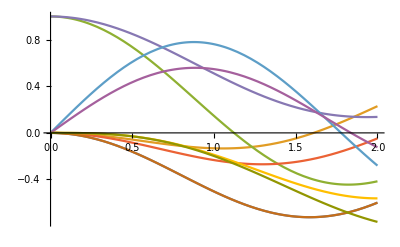

```mathematica
Plot[{Re[Δ[z]]/.sol1,Re[Θ[z]]/.sol1,Re[Γ[z]]/.sol1,Re[Σ[z]]/.sol2,Re[ Π[z]]/.sol2,Re[Δ[z]]/.sol1,Im[Θ[z]]/.sol1,Im[Γ[z]]/.sol1,Im[Σ[z]]/.sol2,Im[ Π[z]]/.sol2},{z,0,2}]
```

```mathematica
Plot[{Re[Δ[z]]/.sol3,Re[Θ[z]]/.sol3,Re[ Γ[z]]/.sol3,Re[Σ[z]]/.sol3,Re[Π[z]]/.sol3,Re[Δ[z]]/.sol3,Im[Θ[z]]/.sol3,Im[ Γ[z]]/.sol3,Im[Σ[z]]/.sol3,Im[Π[z]]/.sol3},{z,0,2}]
```

-Graphics-

### Next, we calculate the prefix functions, ie. the functions that rule the coherent state representation. We can calulate them from the five ‘greeks’ or we get a numerical solution via the set of non-linear differential equations; at the end we compare the results

```mathematica
solCS={μp[z]->(-ⅈ Δ[z])/Γ[z],
ιp[z]->(-ⅈ (-Γ[z]Σ[z]+Δ[z]Θ[z]))/(Δ[z]^2-Γ[z]Π[z]),
νp[z]->(-ⅈ (Δ[z]Σ[z]-Π[z]Θ[z]))/(Δ[z]^2-Γ[z]Π[z]),
y0[z]->3/2 ⅈ Log[Γ[z]],
ι0[z]->2 ⅈ Log[(Γ[z]Π[z]-Δ[z]^2)/Sqrt[Γ[z]]]}
```

{μp[z]→-(ⅈ Δ[z])/Γ[z],ιp[z]→-(ⅈ (Δ[z] Θ[z]-Γ[z] Σ[z]))/(Δ[z]^2-Γ[z] Π[z]),νp[z]→-(ⅈ (-Θ[z] Π[z]+Δ[z] Σ[z]))/(Δ[z]^2-Γ[z] Π[z]),y0[z]→3/2 ⅈ Log[Γ[z]],ι0[z]→2 ⅈ Log[(-Δ[z]^2+Γ[z] Π[z])/(√Γ[z])]}

```mathematica
eq={ιp'(z)==g1 (ιp(z))^2+g1+g2 ιp(z) νp(z)-ⅈ g3 νp(z),μp'(z)==ιp(z) μp(z) (-g1+ⅈ g2 μp(z))+ⅈ g1 νp(z)+g2 μp(z) νp(z)+g3 (μp(z))^2+g3,νp'(z)==g1 ιp(z) νp(z)+g2 (νp(z))^2+g2-ⅈ g3 ιp(z),ι0'(z)==ⅈ (ιp(z) (-2 g1+ⅈ g2 μp(z))-g2 νp(z)+g3 μp(z)),y0'(z)==-3/2 ⅈ (g2 νp(z)+μp(z) (g3+ⅈ g2 ιp(z))),νm'(z)==g2 ⅇ^(1/2 ⅈ (2 y0(z)+ι0(z)))-ⅈ ⅇ^(ⅈ ι0(z)) μm(z) (g1-ⅈ g2 μp(z)),μm'(z)==ⅇ^(ⅈ y0(z)-1/2 ⅈ ι0(z)) (g3+ⅈ g2 ιp(z)),ιm'(z)==ⅇ^(ⅈ ι0(z)) (g1-ⅈ g2 μp(z))};ode = Join[eq,{ιp[0]==0,ι0[0]==0,ιm[0]==0,νp[0]==0,y0[0]==0,νm[0]==0,μp[0]==0,μm[0]==0}];solODE = NDSolve[ode/.{g1->1,g2->(α/.sol[[4]]),g3->(β/.sol[[4]])}, {ιp[z], μp[z],  νp[z],
ι0[z],y0[z],
νm[z], μm[z], ιm[z]},{z,0,50}];
```

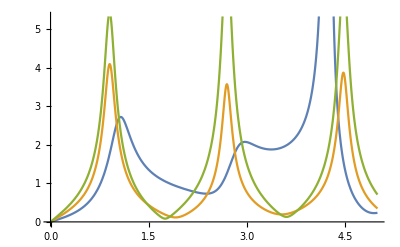

```mathematica
Plot[{Abs[μp[z]]/.solODE,Abs[ιp[z]/.solODE],
Abs[νp[z]/.solODE]},{z,0,5}]
```

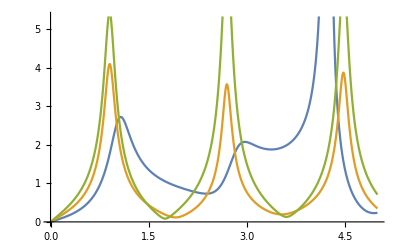

```mathematica
Plot[{Abs[μp[z]]/.solCS/.sol1,Abs[ιp[z]/.solCS/.sol1/.sol2],
Abs[νp[z]/.solCS/.sol1/.sol2]},{z,0,5}]
```

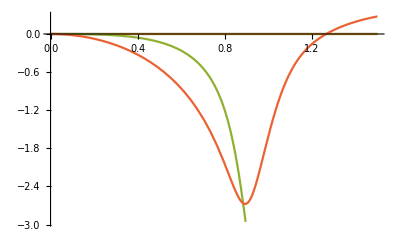

```mathematica
Plot[{0Re[y0[z]]/.solODE,0Im[y0[z]/.solODE],
Re[ι0[z]/.solODE],1Im[ι0[z]/.solODE]},{z,0,1.5}]
```

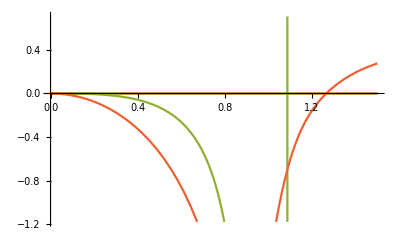

```mathematica
Plot[{0 Re[y0[z]]/.solCS/.sol1/.sol2,0Im[y0[z]/.solCS/.sol1/.sol2],
 Re[ι0[z]/.solCS/.sol1/.sol2],1Im[ι0[z]/.solCS/.sol1/.sol2]},{z,0,1.5}]
```

```mathematica
Finally we want to make sure the coherent state propagator gives the correct result and compare it to the direct propagator
```

```mathematica
U[z_]:=MatrixExp[ⅈ ιp[z] ({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}})].MatrixExp[ⅈ μp[z]({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}})].MatrixExp[ⅈ νp[z]({{0, 0, 1}, {0, 0, 0}, {0, 0, 0}})].MatrixExp[ⅈ ι0[z]({{1/2, 0, 0}, {0, -1/2, 0}, {0, 0, 0}}) ].MatrixExp[ⅈ y0[z]({{1/3, 0, 0}, {0, 1/3, 0}, {0, 0, -2/3}})].MatrixExp[ⅈ νp[z]({{0, 0, 0}, {0, 0, 0}, {1, 0, 0}})].MatrixExp[ⅈ μp[z]({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}})].MatrixExp[ⅈ ιp[z]({{0, 0, 0}, {1, 0, 0}, {0, 0, 0}})];
```

```mathematica
f[z_]:=Abs[ ((U[z]/.solCS/.sol1[[1]]/.sol2[[1]]).({{0.1}, {0.2}, {-0.3}}))];
ParametricPlot3D[f[z] ,{z,0,5}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Abs[MatrixExp[ⅈ H z/.sol[[4]]].({{0.1}, {0.2}, {-0.3}})],{z,0,5} ]
```

-Graphics3D-

```mathematica
N[MatrixExp[ⅈ H z/.sol[[4]]]/.{z->10}]//TraditionalForm
```

(-0.248861+0.0366309 ⅈ | 0.262678+0.330381 ⅈ | 0.514481+0.702769 ⅈ
0.262678+0.330381 ⅈ | 0.227222+0.816509 ⅈ | -0.143239-0.288122 ⅈ
0.514481+0.702769 ⅈ | -0.143239-0.288122 ⅈ | -0.0463046+0.368441 ⅈ)

```mathematica
N[(U[z]/.solCS/.sol1[[1]]/.sol2[[1]])/.{z->10}]//TraditionalForm
```

(-0.248861+0.0366309 ⅈ | 0.262678+0.330381 ⅈ | 0.514481+0.702769 ⅈ
0.262678+0.330381 ⅈ | 0.227222+0.816509 ⅈ | -0.143239-0.288122 ⅈ
0.514481+0.702769 ⅈ | -0.143239-0.288122 ⅈ | -0.0463046+0.368441 ⅈ)